# The effect of open access on research quality

## Model

### Quality and Journals

2 journals

article quality, omega: 0 =< omega <= 1.

cutoff quality, q1 and q2, q1 > q2.
雑誌1はqualityがq1以上の論文を採択、雑誌2はq2以上q1未満の論文を採択

### Open access

A model of max profits :

収入: APCに依存、即ち論文数に依存するため、雑誌は採択論文数（n1,n2）を最大化する

論文数の比: n1=1-q1、n2=q1-q2 。

平衡状態: 予想される平衡状態は、q1=0.5、q2=0で両者が同じ収入になる。

投稿者から見た採択の確率: どちらかの雑誌に採択される確率が100%になる。

### Restricted access

収入: [読者数] x [雑誌価格]と仮定すると、読者は[質]x[量]を適正価格と評価する。これによれば、雑誌1の収入Ri=oi^alp ni^(1-alp)、oiは論文の平均品質、niは論文数、alpは重み。
o1=(1+q1)/2; n1=1-q1; R1=((1+q1)/2)^alp * (1-q1)^(1-alp);
o2=(q1+q2)/2; n2=q1-q2; R2=((q1+q2)/2)^alp * (q1-q2)^(1-alp).

論文数の比: n1=1-q1、n2=q1-q2 。

平衡状態: q1=1/Sqrt(2)=0.71、q2=0。

投稿者から見た採択の確率: どちらかの雑誌に採択される確率が100%になる。

```mathematica
R[1]=((1+q1)/2)^alp*(1-q1)^(1-alp) (*income of journal1*)
R[2]=((q1+q2)/2)^alp*(q1-q2)^(1-alp) (*income of journal2*)
```

2^-alp (1-q1)^(1-alp) (1+q1)^alp

2^-alp (q1-q2)^(1-alp) (q1+q2)^alp

```mathematica
r1=R[1]/.alp->1/2//Simplify
```

(√(1-q1^2))/(√2)

```mathematica
r2=R[2]/.alp->1/2//Simplify
```

(√(q1-q2) √(q1+q2))/(√2)

Plot

```mathematica
p1=Table[NSolve[(R[1]==R[2]/.{alp:>i,q2->0}),{q1},Reals],{i,0,1,0.02}]
```

{{{q1→0.5}},{{q1→0.505567}},{{q1→0.511288}},{{q1→0.517167}},{{q1→0.523213}},{{q1→0.529434}},{{q1→0.535836}},{{q1→0.542429}},{{q1→0.549221}},{{q1→0.556222}},{{q1→0.563442}},{{q1→0.570892}},{{q1→0.578583}},{{q1→0.586526}},{{q1→0.594736}},{{q1→0.603225}},{{q1→0.612008}},{{q1→0.6211}},{{q1→0.630518}},{{q1→0.640278}},{{q1→0.650398}},{{q1→0.660899}},{{q1→0.671799}},{{q1→0.683119}},{{q1→0.694881}},{{q1→0.707107}},{{q1→0.719818}},{{q1→0.733035}},{{q1→0.74678}},{{q1→0.76107}},{{q1→0.775919}},{{q1→0.791335}},{{q1→0.807318}},{{q1→0.823854}},{{q1→0.840909}},{{q1→0.858421}},{{q1→0.876291}},{{q1→0.894364}},{{q1→0.91241}},{{q1→0.930105}},{{q1→0.946999}},{{q1→0.962512}},{{q1→0.975951}},{{q1→0.986606}},{{q1→0.993972}},{{q1→0.998068}},{{q1→0.999656}},{{q1→0.999981}},{{q1→1.}},{{q1→1.}},{}}

Part::partw: {}の部分1は存在しません．

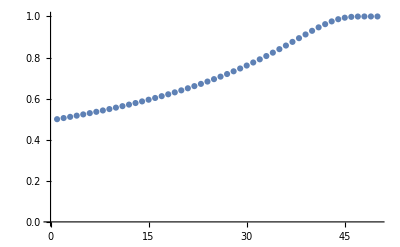

```mathematica
Map[#[[1,1,2]]&,p1]//ListPlot
```

```mathematica
p1=Table[NSolve[(R[1]==R[2]/.{alp:>i,q2->j}),{q1},Reals],{j,0,1,0.05},{i,0,1,0.02}];
```

```mathematica
p1//Dimensions
```

{21,51}

```mathematica
p1[[1]]
```

{{{q1→0.5}},{{q1→0.505567}},{{q1→0.511288}},{{q1→0.517167}},{{q1→0.523213}},{{q1→0.529434}},{{q1→0.535836}},{{q1→0.542429}},{{q1→0.549221}},{{q1→0.556222}},{{q1→0.563442}},{{q1→0.570892}},{{q1→0.578583}},{{q1→0.586526}},{{q1→0.594736}},{{q1→0.603225}},{{q1→0.612008}},{{q1→0.6211}},{{q1→0.630518}},{{q1→0.640278}},{{q1→0.650398}},{{q1→0.660899}},{{q1→0.671799}},{{q1→0.683119}},{{q1→0.694881}},{{q1→0.707107}},{{q1→0.719818}},{{q1→0.733035}},{{q1→0.74678}},{{q1→0.76107}},{{q1→0.775919}},{{q1→0.791335}},{{q1→0.807318}},{{q1→0.823854}},{{q1→0.840909}},{{q1→0.858421}},{{q1→0.876291}},{{q1→0.894364}},{{q1→0.91241}},{{q1→0.930105}},{{q1→0.946999}},{{q1→0.962512}},{{q1→0.975951}},{{q1→0.986606}},{{q1→0.993972}},{{q1→0.998068}},{{q1→0.999656}},{{q1→0.999981}},{{q1→1.}},{{q1→1.}},{}}

```mathematica
(p1d=Map[Drop[#,-1]&,p1])//Dimensions
```

{21,50}

```mathematica
(v1d=Map[#[[1,1,2]]&,p1d,{2}])//Dimensions
```

{21,50}

```mathematica
ListPointPlot3D[v1d]
```

-Graphics3D-

Eq

```mathematica
sAlp=Range[0,1,0.05];eqs=Table[{R[1]==R[2]},{alp,0,1,0.05}](*sliding alp*)
```

{{1. (1-q1)^1.==1. (q1-q2)^1.},{0.965936 (1-q1)^0.95 (1+q1)^0.05==0.965936 (q1-q2)^0.95 (q1+q2)^0.05},{0.933033 (1-q1)^0.9 (1+q1)^0.1==0.933033 (q1-q2)^0.9 (q1+q2)^0.1},{0.90125 (1-q1)^0.85 (1+q1)^0.15==0.90125 (q1-q2)^0.85 (q1+q2)^0.15},{0.870551 (1-q1)^0.8 (1+q1)^0.2==0.870551 (q1-q2)^0.8 (q1+q2)^0.2},{0.840896 (1-q1)^0.75 (1+q1)^0.25==0.840896 (q1-q2)^0.75 (q1+q2)^0.25},{0.812252 (1-q1)^0.7 (1+q1)^0.3==0.812252 (q1-q2)^0.7 (q1+q2)^0.3},{0.784584 (1-q1)^0.65 (1+q1)^0.35==0.784584 (q1-q2)^0.65 (q1+q2)^0.35},{0.757858 (1-q1)^0.6 (1+q1)^0.4==0.757858 (q1-q2)^0.6 (q1+q2)^0.4},{0.732043 (1-q1)^0.55 (1+q1)^0.45==0.732043 (q1-q2)^0.55 (q1+q2)^0.45},{0.707107 (1-q1)^0.5 (1+q1)^0.5==0.707107 (q1-q2)^0.5 (q1+q2)^0.5},{0.68302 (1-q1)^0.45 (1+q1)^0.55==0.68302 (q1-q2)^0.45 (q1+q2)^0.55},{0.659754 (1-q1)^0.4 (1+q1)^0.6==0.659754 (q1-q2)^0.4 (q1+q2)^0.6},{0.63728 (1-q1)^0.35 (1+q1)^0.65==0.63728 (q1-q2)^0.35 (q1+q2)^0.65},{0.615572 (1-q1)^0.3 (1+q1)^0.7==0.615572 (q1-q2)^0.3 (q1+q2)^0.7},{0.594604 (1-q1)^0.25 (1+q1)^0.75==0.594604 (q1-q2)^0.25 (q1+q2)^0.75},{0.574349 (1-q1)^0.2 (1+q1)^0.8==0.574349 (q1-q2)^0.2 (q1+q2)^0.8},{0.554785 (1-q1)^0.15 (1+q1)^0.85==0.554785 (q1-q2)^0.15 (q1+q2)^0.85},{0.535887 (1-q1)^0.1 (1+q1)^0.9==0.535887 (q1-q2)^0.1 (q1+q2)^0.9},{0.517632 (1-q1)^0.05 (1+q1)^0.95==0.517632 (q1-q2)^0.05 (q1+q2)^0.95},{0.5 (1+q1)^1.==0.5 (q1+q2)^1.}}

```mathematica
FindMaximum[{eqs[[1,1,1]],q1≤1,q1≥0},{q1}]
```

{1.,{q1→0.}}

```mathematica
q1FindMaxIncome=Map[FindMaximum[{#[[1,1]],q1≤1,q1≥0},{q1}]&,eqs]
```

{{1.,{q1→0.}},{0.965936,{q1→9.45772×10^-8}},{0.933033,{q1→1.11811×10^-7}},{0.90125,{q1→1.34114×10^-7}},{0.87055,{q1→1.6407×10^-7}},{0.840896,{q1→2.06271×10^-7}},{0.812252,{q1→2.69924×10^-7}},{0.784584,{q1→3.76698×10^-7}},{0.757858,{q1→6.41212×10^-7}},{0.732043,{q1→1.62055×10^-6}},{0.707106,{q1→0.00109759}},{0.68645,{q1→0.100001}},{0.673173,{q1→0.2}},{0.66708,{q1→0.3}},{0.668365,{q1→0.4}},{0.677702,{q1→0.5}},{0.69644,{q1→0.6}},{0.727067,{q1→0.7}},{0.774321,{q1→0.8}},{0.848863,{q1→0.9}},{1.,{q1→1.}}}

```mathematica
q1FindMaxIncome[[1,2,1]]
```

q1→0.

```mathematica
eqs[[1,1]]/.q1FindMaxIncome[[1,2,1]]
```

1.==1. (0.-q2)^1.

```mathematica
eqs[[2,1]]/.q1FindMaxIncome[[2,2,1]]
```

0.965936==0.965936 (9.45772×10^-8-q2)^0.95 (9.45772×10^-8+q2)^0.05

```mathematica
sAlp[[3]]
```

0.1

```mathematica
NSolve[eqs[[3,1]]/.q1FindMaxIncome[[3,2,1]],{q2}]
```

{{q2→-0.951056-0.309017 ⅈ},{q2→-0.951056+0.309017 ⅈ}}

```mathematica
sAlp[[11]]
```

0.5

```mathematica
NSolve[eqs[[11,1]]/.q1FindMaxIncome[[11,2,1]],{q2}]
```

{{q2→0.-0.999999 ⅈ},{q2→0.+0.999999 ⅈ}}

```mathematica
sAlp[[13]]
```

0.6

```mathematica
NSolve[eqs[[13,1]]/.q1FindMaxIncome[[13,2,1]],{q2}]
```

{{q2→0.280407-0.951833 ⅈ},{q2→0.280407+0.951833 ⅈ}}

```mathematica
sAlp[[21]]
```

1.

```mathematica
NSolve[eqs[[21,1]]/.q1FindMaxIncome[[21,2,1]],{q2}]
```

{{q2→1.}}

## Code Example

```mathematica
FindMaximum[{s+t,s≥1,s≤3,t==s},{s,t}]
```

{6.,{s→3.,t→3.}}